```mathematica
Quit[]
```

```mathematica
p[r_]:=1/(56 π r^2)
```

```mathematica
m[r_]:=12 π ∫_ϵ^r (p[t] t^2)ⅆt
```

```mathematica
m[r]
```

(3 (r-ϵ))/14

```mathematica
g[r_]:=(m[r]+4 π p[r] r^3)/(r^2(1-(2 m[r])/r))
```

```mathematica
g[r]//FullSimplify
```

(m[r]+4 π r^3 p[r])/(r^2-2 r m[r])

```mathematica
Assuming[0<ϵ<r,FullSimplify[Exp[-2 ∫_ϵ^r g[t]ⅆt]]]
```

ⅇ^(-2 ∫_ϵ^r (m[t]+4 π t^3 p[t])/(t^2-2 t m[t])ⅆt)

```mathematica
int[r_]:=(49 r ϵ)/(4 r+3 ϵ)^2
```

```mathematica
Assuming[0<ϵ<r,FullSimplify[(k √(1-(2 m[r])/r) int[r])/(1+ 4 π k ∫_ϵ^r ((t int[t])/(√(1-(2 m[t])/t)))ⅆt)]]
```

(49 k ϵ √(r (r-2 m[r])))/((4 r+3 ϵ)^2 (1+4 k π ∫_ϵ^r (49 t^2 ϵ)/((4 t+3 ϵ)^2 √(1-(2 m[t])/t))ⅆt))

```mathematica
Clear[dp]
```

```mathematica
dp[r_,ϵ_,k_]:=(7 √7 k r ϵ √(4+(3 ϵ)/r))/((4 r+3 ϵ)^2 (1-3/32 √7 k π ϵ^(3/2) (94 √7 √ϵ-(98 √(r/ϵ) (16 r^2+80 r ϵ+45 ϵ^2))/(3 (4 r+3 ϵ)^(3/2))-245 √ϵ ArcSinh[2/(√3)]+245 √ϵ ArcSinh[(2 √(r/ϵ))/(√3)])))
```

```mathematica
Limit[dp[5,ϵ,-0.1],ϵ->0]
```

0.

```mathematica
Plot[{p[r],p[r]+dp[r,0.001,-0.5]},{r,0.1,20},AxesOrigin->{0,0}]
```

-Graphics-

```mathematica
NSolve[p[10]+dp[10,0.001,k]==0,k]
```

{{k→-(3.12653×10^17 p[10])/(7.2372×10^13+1.58907×10^17 p[10])}}

```mathematica
Assuming[0<ϵ<r,FullSimplify[Limit[p[r]+dp[r,ϵ,k],r->ϵ]]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

```mathematica
FullSimplify[Solve[k+1/(56 π ϵ^2)==A,k]/.r->ϵ]
```

{{k→A-1/(56 π ϵ^2)}}

```mathematica
Series[p[r]+dp[r,ϵ,k],{r,ϵ,2}]
```

(k+1/(56 π ϵ^2))+(-4 k^2 π-1/(28 π ϵ^3)-(5 k)/(14 ϵ)) (r-ϵ)+(16 k^3 π^2+3/(56 π ϵ^4)+(23 k)/(392 ϵ^2)+(9 k^2 π)/(7 ϵ)) (r-ϵ)^2+O[r-ϵ]^3

```mathematica
k1[A_,ϵ_]:=A-1/(56 π ϵ^2);
```

```mathematica
Clear[A,ϵ,k,k1]
```

```mathematica
A=100;
ϵ=0.01;
k1[A,ϵ]
```

43.1589

```mathematica
p[100]+dp[100,ϵ,k1[A,ϵ]]
```

0.0000567716

9.43159×10^6

1.×10^7

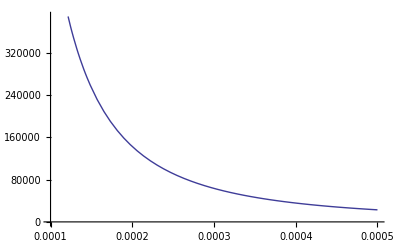

```mathematica
A=10000000;
ϵ=0.0001;
k1[A_,ϵ_]:=A-1/(56 π ϵ^2);
k1[A,ϵ]
p[ϵ]+dp[ϵ,ϵ,k1[A,ϵ]]
Plot[{p[r]+dp[r,ϵ,k1[A,ϵ]]},{r,ϵ,5ϵ},AxesOrigin->{ϵ,0}]
Clear[A,ϵ,k,k1];
```

```mathematica
(* CHECKS *)
```

```mathematica
Solve[(4(P-c) (M+4 π P r^3+4/3 π c r^3+4 π c r^3))/(r^2(1-(2 M)/r-(8 π c r^2)/3))==(4(P) (M+4 π P r^3))/(r^2(1-(2 M)/r)),c]//FullSimplify
```

{{c→0},{c→(-6 M^2+3 M r-4 P π r^4 (1+8 P π r^2))/(16 π (2 M-r) r^3)}}

```mathematica
(-6 m[r]^2+3 m[r] r-4 p[r] π r^4 (1+8 p[r] π r^2))/(16 π (2 m[r]-r) r^3)/.ϵ->0//FullSimplify
```

-1/(32 π r^2)

```mathematica
(4p[r] (m[r]+4 π p[r] r^3))/(r^2(1-(2 m[r])/r))/.ϵ->0//FullSimplify
-p'[r]//FullSimplify
```

1/(28 π r^3)

1/(28 π r^3)

```mathematica
(* REPEAT THE PROCESS *)
```

```mathematica
k2=A-1/(56 π ϵ^2);
```

```mathematica
12 π ∫_ϵ^r (((k2+1/(56 π ϵ^2))+(-4 k2^2 π-1/(28 π ϵ^3)-(5 k2)/(14 ϵ)) (r-ϵ)+(16 k2^3 π^2+3/(56 π ϵ^4)+(23 k2)/(392 ϵ^2)+(9 k2^2 π)/(7 ϵ)) (r-ϵ)^2) r^2)ⅆr//FullSimplify
```

1/(54880 ϵ^6)(6 r^5 (-2+ϵ (9+ϵ (1153+56 A π (6+ϵ (-18+ϵ (23+56 A π (-6+ϵ (9+112 A π ϵ))))))))-15 r^4 ϵ (-2+ϵ (23+ϵ (1475+56 A π (6+ϵ (-46+ϵ (93+56 A π (-6+ϵ (23+112 A π ϵ))))))))+10 r^3 ϵ^2 (-2+ϵ (37+ϵ (1797+56 A π (6+ϵ (-74+ϵ (555+56 A π (-6+ϵ (37+112 A π ϵ))))))))+ϵ^5 (2+ϵ (-79+ϵ (-2763-56 A π (6+ϵ (-158+ϵ (4293+56 A π (-6+ϵ (79+112 A π ϵ)))))))))

```mathematica
Assuming[0<ϵ<r,m2[r]]
```

$Aborted